# Single group projection operators

## Basis Functions

```mathematica
Xb[r_,θ_,ϕ_]:=1/(√2)(SphericalHarmonicY[1,-1,θ,ϕ]-SphericalHarmonicY[1,1,θ,ϕ]);
Yb[r_,θ_,ϕ_]:=-I/(√2)(SphericalHarmonicY[1,-1,θ,ϕ]+SphericalHarmonicY[1,1,θ,ϕ]);
Zb[r_,θ_,ϕ_]:=SphericalHarmonicY[1,0,θ,ϕ];
```

## Generate test data

```mathematica
(*test function considered here is independent of the radial coordinate. Fix the radial coordinate to R*)
ρ=√(x^2+y^2+z^2);

test[x_,y_,z_]:=Zb[ρ,ArcCos[z/ρ],ArcTan[y/x]];
T=Flatten[Table[{{x,y,z},test[x,y,z]},{x,-0.5,0.5,1/21},{y,-0.5,0.5,1/21},{z,-0.5,0.5,1/21}],2];
```

## Applying projection Operators

```mathematica
h=3;
L=24;
```

```mathematica
A=Table[Interpolation[Table[{Rm[j].T[[i,1]],h/L*R[j][[m,n]]**T[[i,2]]},{i,1,Length[T]}]],{m,1,3},{n,1,3} ,{j,1,24}];
B[m_,n_,x_,y_,z_]:=Sum[A[[m,n]][[j]][x,y,z],{j,1,L}]
AR[m_,n_,r_,θ_,ϕ_]:=B[m,n,r*Sin[θ]*Cos[ϕ],r*Sin[θ]*Sin[ϕ],r*Cos[θ]];
```

### Note: m,n label the projection from state m to state n for the input state Zb

## Projections - showing plots are the same as expected

### Zb ->Zb

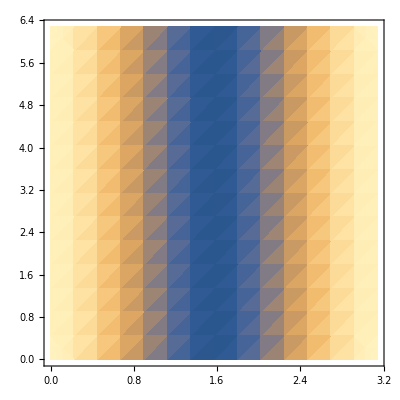

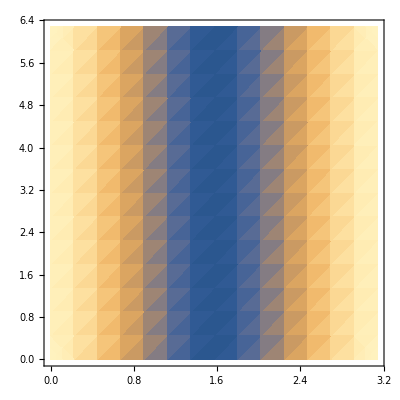

```mathematica
DensityPlot[Abs[AR[3,3,0.1,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π}]
DensityPlot[Abs[Zb[0.1,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π}]
```

### Zb ->Yb

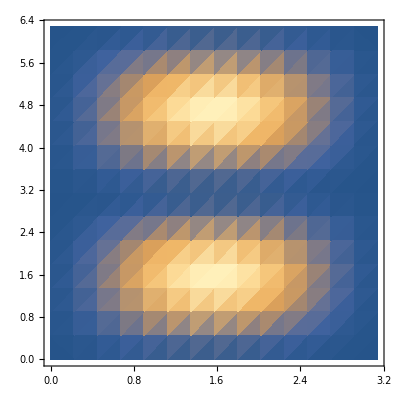

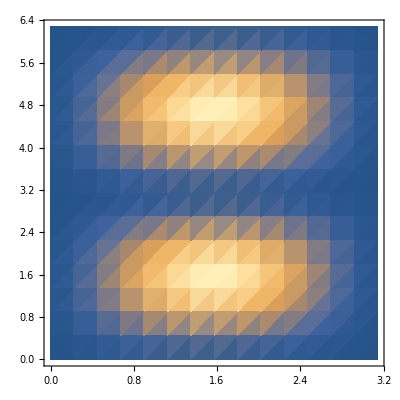

```mathematica
DensityPlot[Abs[AR[3,2,0.1,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π}]
DensityPlot[Abs[Yb[0.1,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π}]
```

### Zb ->Xb

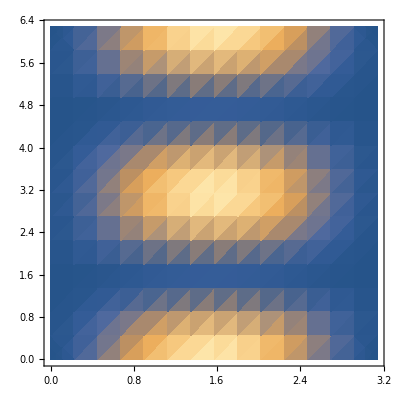

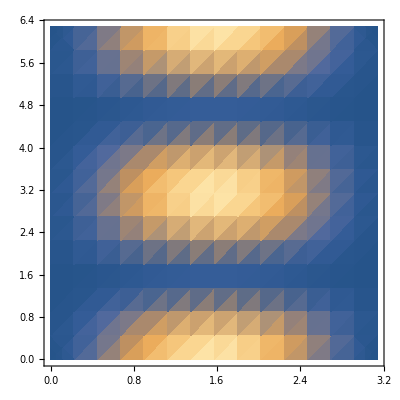

```mathematica
DensityPlot[Abs[AR[3,1,0.1,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π}]
DensityPlot[Abs[Xb[0.1,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π}]
```

### Xb ->Xb

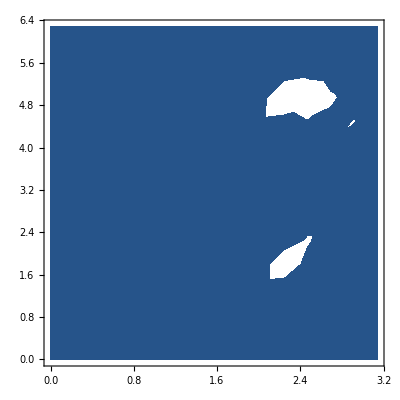

-Graphics-

```mathematica
DensityPlot[Abs[AR[1,1,0.1,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π}]
DensityPlot[Abs[Xb[0.1,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π}]
```